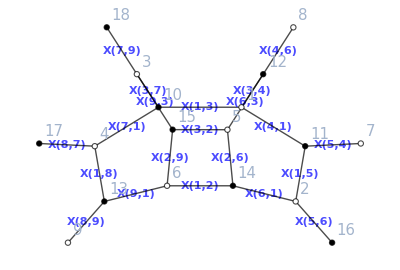

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=28;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
(*This is to fix my functional tests*)
```

```mathematica
perfs=perfectMatchings[a,b,c,d];
Cmatrix=getGrassmannian[a,b,c,d];

If[Cmatrix=!=Null,
sources=findSources[b,c,perfs[[lowNumberLoopsPM[a,b,c,d]]]];
sinks=findSinks[b,c,perfs[[lowNumberLoopsPM[a,b,c,d]]]];
If[Dimensions[Cmatrix]=!={Length[sources],Length[Join[sources,sinks]]},
Print["ii=",ii," : There's a problem with the Grassmannian matrix! Its size is not correct!"];
];
variablesmatrix=Map[Intersection[Variables[#],Variables[Join[b,c]]]&,Cmatrix,{2}];

If[((Sort[Flatten[Map[DeleteDuplicates[Join@@#]&,Map[Intersection[#,sources]&,variablesmatrix,{2}]]]]===Sort[sources])&&(Sort[Flatten[Map[DeleteDuplicates[Join@@#]&,Map[Intersection[#,sinks]&,Transpose[variablesmatrix],{2}]]]]===Sort[sinks]))=!=True,
Print["ii=",ii," : There's a problem with the Grassmannian matrix! It doesn't seem to be going from sources to sinks"];
];
minors=Expand[Simplify[Minors[Cmatrix,Length[Cmatrix]][[1]]]];
If[Position[minors,Power[___,2]|Power[___,3]|Power[___,4]|Times[2,___]|Times[3,___]|Times[4,___]]=!={},
Print["ii=",ii," : There's a problem with the Grassmannian matrix! Its minors do not simplify"];
];
];
```

ii=28 : There's a problem with the Grassmannian matrix! Its minors do not simplify

```mathematica
Cmatrix//MatrixForm
```

(X[1,8]/(X[8,7] X[8,9])+(X[3,2] X[3,4] X[7,1] X[9,1])/(X[1,3] X[2,9] X[6,3] X[8,7] X[8,9]) | 1 | 0 | -(X[2,6] X[3,4] X[5,6] X[7,1])/(X[1,3] X[6,1] X[6,3] X[8,7])-(X[1,2] X[3,2] X[3,4] X[5,6] X[7,1])/(X[1,3] X[2,9] X[6,1] X[6,3] X[8,7]) | (X[4,1] X[7,1])/(X[1,3] X[5,4] X[8,7])-(X[1,5] X[2,6] X[3,4] X[7,1])/(X[1,3] X[5,4] X[6,1] X[6,3] X[8,7])-(X[1,2] X[1,5] X[3,2] X[3,4] X[7,1])/(X[1,3] X[2,9] X[5,4] X[6,1] X[6,3] X[8,7]) | 0
-(X[3,2] X[3,4] X[3,7] X[9,1])/(X[1,3] X[2,9] X[6,3] X[7,9] X[8,9])-(X[9,1] X[9,3])/(X[2,9] X[7,9] X[8,9]) | 0 | 1 | -(X[2,6] X[3,4] X[3,7] X[5,6])/(X[1,3] X[6,1] X[6,3] X[7,9])-(X[1,2] X[3,2] X[3,4] X[3,7] X[5,6])/(X[1,3] X[2,9] X[6,1] X[6,3] X[7,9])-(X[1,2] X[5,6] X[9,3])/(X[2,9] X[6,1] X[7,9]) | (X[3,7] X[4,1])/(X[1,3] X[5,4] X[7,9])-(X[1,5] X[2,6] X[3,4] X[3,7])/(X[1,3] X[5,4] X[6,1] X[6,3] X[7,9])-(X[1,2] X[1,5] X[3,2] X[3,4] X[3,7])/(X[1,3] X[2,9] X[5,4] X[6,1] X[6,3] X[7,9])-(X[1,2] X[1,5] X[9,3])/(X[2,9] X[5,4] X[6,1] X[7,9]) | 0
-(X[3,2] X[4,6] X[9,1])/(X[2,9] X[6,3] X[8,9]) | 0 | 0 | -(X[2,6] X[4,6] X[5,6])/(X[6,1] X[6,3])-(X[1,2] X[3,2] X[4,6] X[5,6])/(X[2,9] X[6,1] X[6,3]) | -(X[1,5] X[2,6] X[4,6])/(X[5,4] X[6,1] X[6,3])-(X[1,2] X[1,5] X[3,2] X[4,6])/(X[2,9] X[5,4] X[6,1] X[6,3]) | 1)

```mathematica
(*This is to fix the makeAutomaticBoundariesAndCuts function*)
```

```mathematica
adjacencymat=getAdjacencyMatrix[topleft,topright,bottomleft,bottomright];
graph=AdjacencyGraph[adjacencymat];(*We have finished making the Mathematica graph!*)
```

```mathematica
makeAutomaticBoundariesAndCuts[graph,topleft,topright,bottomleft,bottomright]
```

{{{X[8,9]},{X[8,7]},{X[7,9]},{X[5,6]},{X[5,4]},{X[4,6]}},{{{X[8,9]},{X[8,7]}}→{},{{X[8,7]},{X[7,9]}}→{X[7,1]→-X[7,1],X[1,8]→-X[1,8]},{{X[7,9]},{X[5,6]}}→{X[9,3]→-X[9,3],X[6,3]→-X[6,3],X[5,4]→-X[5,4],X[4,6]→-X[4,6]},{{X[5,6]},{X[5,4]}}→{X[5,4]→-X[5,4]},{{X[5,4]},{X[4,6]}}→{X[2,6]→-X[2,6],X[3,2]→-X[3,2]}}}

```mathematica
planargraph=Graph[graph,GraphLayout->"PlanarEmbedding"];
verticespos=MapThread[{#1,#2}&,{Range[Length[GraphEmbedding[planargraph]]],GraphEmbedding[planargraph]}];
edgepos=Map[{{verticespos[[#[[1]],2]],verticespos[[#[[2]],2]]},#}&,EdgeList[planargraph]];
edgepos=DeleteDuplicates[edgepos];(*in case there are bubbles*)
(*Now we have the vertices and edges for an embedding with no edge crossings*)
(*Each external vertex will be seen as having its own tiny boundary attached to it*)
boundaries=Transpose[{Flatten[DeleteCases[Join[bottomleft,Transpose[topright]],0,{2}]]}];
(*Now we'll construct the cuts: they will run directly between the external vertices, since the boundaries are so tiny*)
externalnodenumbers=Join[Range[Length[bottomleft]]+Length[topleft],Range[Dimensions[topright][[2]]]+Total[Dimensions[topleft]]+Length[bottomleft]];
(*Now decrease the length of all external edges by about 14%, since PlanarEmbedding tries to put everything as collinear as possible, which is problematic when we make cuts*)
verticestocoords=Map[Rule@@#&,verticespos];
externalvertices=externalnodenumbers/.verticestocoords;
externaledges=Cases[edgepos,{___,UndirectedEdge[Alternatives@@externalnodenumbers,_]}|{___,UndirectedEdge[_,Alternatives@@externalnodenumbers]}];
decreaseExternalEdgeLength=Function[{inputedge,decreasequantity},
(*This function needs externalvertices to be accurate in order to work*)
Block[{tosubtractcoords,externalnodepolarcoords,newposition,newpositionrule},
tosubtractcoords=Cases[inputedge[[1]],Except[Alternatives@@externalvertices]][[1]];
externalnodepolarcoords=ToPolarCoordinates[DeleteCases[Map[#-tosubtractcoords&,inputedge[[1]]],{0.,0.}][[1]]];
newposition=tosubtractcoords+FromPolarCoordinates[{(1.-decreasequantity)externalnodepolarcoords[[1]],externalnodepolarcoords[[2]]}];
newpositionrule=Cases[inputedge[[1]],Except[tosubtractcoords]][[1]]->newposition;
newpositionrule]
];
shiftexternaledges=Map[decreaseExternalEdgeLength[#,0.14]&,externaledges];
verticespos=verticespos/.shiftexternaledges;
edgepos=edgepos/.shiftexternaledges;
verticestocoords=Map[Rule@@#&,verticespos];
externalvertices=externalvertices/.shiftexternaledges;
externaledges=externaledges/.shiftexternaledges;
(*Now we have the vertices and edges for an embedding with no edge crossings.*)
(*Now we'll construct the cuts: they will run directly between the external vertices, since the boundaries are so tiny*)
(*We'll make a sequence of boundaries connected by cuts. We'll start with the external node with the highest y-coordinate, and proceed along external nodes as we spiral in to the middle. This ensures that the cuts never cross each other*)
(*Before we start we'll make a rule that translates node numbers into edge labels. This will be useful to us at the very end*)
nodenumberstoedges=MapThread[Rule,{externalnodenumbers,Flatten[boundaries]}];
(*This function takes a list of vertices and orders them according to the spiralling-in order*)
spiralInList=Function[{vertexlist},
Block[{remainingvertices,nextnode,finalvertexlist,polardistances},
remainingvertices=vertexlist;
(*The first node is the one with the largest y-coordinate*)
nextnode=Cases[remainingvertices,{_,Max[Map[#[[2]]&,remainingvertices]]}][[1]];
finalvertexlist={nextnode};
remainingvertices=DeleteCases[remainingvertices,nextnode];
While[remainingvertices=!={},
polardistances=Map[{#[[1]],Mod[#[[2]],2Pi]}&,Map[ToPolarCoordinates[#-nextnode]&,remainingvertices]];
(*The next node is the first one reached going radially and clockwise from the current node*)
nextnode=Cases[polardistances,{_,Max[Map[#[[2]]&,polardistances]]}];
(*If there are multiple ones with the same angle, pick the nearest one*)
nextnode=Cases[nextnode,{Min[Map[#[[1]]&,nextnode]],_}][[1]];
nextnode=remainingvertices[[Position[polardistances,nextnode][[1,1]]]];
finalvertexlist=Append[finalvertexlist,nextnode];
remainingvertices=DeleteCases[remainingvertices,nextnode];
];
finalvertexlist]
];
(*Now we'll order our external vertices and our boundaries in this new order*)
externalvertices=spiralInList[externalvertices];
boundaries=Map[{#}&,externalvertices/.Map[#[[2]]->#[[1]]&,verticestocoords]]/.nodenumberstoedges;
(*We may now form the cuts: they are (n-1) sequential pairs of externalvertices. We need to see if any of the cuts end up going through nodes attached to external nodes. If they do, things get complicated so it's better to rotate the external node to make sure to cut doesn't do this.*)
cutcoordinates=Table[{externalvertices[[iii]],externalvertices[[iii+1]]},{iii,Length[externalvertices]-1}]
```

{{{5.26598×10^-17,15.86},{12.,4.86}},{{12.,4.86},{11.72,2.86}},{{11.72,2.86},{0.86,4.}},{{0.86,4.},{6.42,3.58}},{{6.42,3.58},{1.28,4.72}}}

```mathematica
(*These cells we'll need to delete -------->        ---------------->       ---------------->       ----------------> *)
```

```mathematica
(*We shall begin by drawing out the graph such that no edges cross. In so doing we'll be able to extract the vertex coordinates and edge positions of this embedding*)
planargraph=Graph[graph,GraphLayout->"PlanarEmbedding"];
verticespos=MapThread[{#1,#2}&,{Range[Length[GraphEmbedding[planargraph]]],GraphEmbedding[planargraph]}];
edgepos=Map[{{verticespos[[#[[1]],2]],verticespos[[#[[2]],2]]},#}&,EdgeList[planargraph]];
edgepos=DeleteDuplicates[edgepos];(*in case there are bubbles*)
(*Now we have the vertices and edges for an embedding with no edge crossings*)
(*Each external vertex will be seen as having its own tiny boundary attached to it*)
boundaries=Transpose[{Flatten[DeleteCases[Join[bottomleft,Transpose[topright]],0,{2}]]}];
(*Now we'll construct the cuts: they will run directly between the external vertices, since the boundaries are so tiny*)
externalnodenumbers=Join[Range[Length[bottomleft]]+Length[topleft],Range[Dimensions[topright][[2]]]+Total[Dimensions[topleft]]+Length[bottomleft]];
externaledges=Cases[edgepos,{___,UndirectedEdge[Alternatives@@externalnodenumbers,_]}|{___,UndirectedEdge[_,Alternatives@@externalnodenumbers]}];
verticestocoords=Map[Rule@@#&,verticespos];
externalvertices=externalnodenumbers/.verticestocoords;
(*Now we'll need to make a sequence of boundaries connected by cuts. We'll start with the external node with the highest y-coordinate, and proceed along external nodes as we spiral in to the middle. This ensures that the cuts never cross each other*)
(*Before we start we'll make a rule that translates node numbers into edge labels. This will be useful to us at the very end*)
nodenumberstoedges=MapThread[Rule,{externalnodenumbers,Flatten[boundaries]}];
(*This function takes a list of vertices and orders them according to the spiralling-in order*)
spiralInList=Function[{vertexlist},
Block[{remainingvertices,nextnode,finalvertexlist,polardistances},
remainingvertices=vertexlist;
(*The first node is the one with the largest y-coordinate*)
nextnode=Cases[remainingvertices,{_,Max[Map[#[[2]]&,remainingvertices]]}][[1]];
finalvertexlist={nextnode};
remainingvertices=DeleteCases[remainingvertices,nextnode];
While[remainingvertices=!={},
polardistances=Map[{#[[1]],Mod[#[[2]],2Pi]}&,Map[ToPolarCoordinates[#-nextnode]&,remainingvertices]];
(*The next node is the first one reached going radially and clockwise from the current node*)
nextnode=Cases[polardistances,{_,Max[Map[#[[2]]&,polardistances]]}];
(*If there are multiple ones with the same angle, pick the nearest one*)
nextnode=Cases[nextnode,{Min[Map[#[[1]]&,nextnode]],_}][[1]];
nextnode=remainingvertices[[Position[polardistances,nextnode][[1,1]]]];
finalvertexlist=Append[finalvertexlist,nextnode];
remainingvertices=DeleteCases[remainingvertices,nextnode];
];
finalvertexlist]
];
(*Now we'll order our external vertices and our boundaries in this new order*)
externalvertices=spiralInList[externalvertices];
boundaries=Map[{#}&,externalvertices/.Map[#[[2]]->#[[1]]&,verticestocoords]]/.nodenumberstoedges;
(*We may now form the cuts: they are (n-1) sequential pairs of externalvertices*)
cutcoordinates=Table[{externalvertices[[iii]],externalvertices[[iii+1]]},{iii,Length[externalvertices]-1}];
```

```mathematica
rotateExternalVertices[]=Module[{},
(*Our cuts may never go through the "critical nodes", i.e.  those nodes attached to external nodes*)
tocriticalnode=Map[Rule@@#&,Join[Map[#[[1]]&,externaledges],Map[Reverse[#[[1]]]&,externaledges]]];
(*If we go through a critical node we need to take the external edges and rotate them. We must stay within the same face and also not cross any other edges.*)
badexternalnodes=Map[cutcoordinates[[Sequence@@#]]&,Position[Map[Table[Solve[#[[1]]+param(#[[2]]-#[[1]])==(#[[iii]]/.tocriticalnode),param]==={},{iii,2}]&,cutcoordinates],False]];
(*This function takes an external edge, finds the two nearest edges to it (coming from the same critical node), determines which ones has the smallest angle to our external edge, and rotates the external edge 95% (to the power "iteration") of the way there*)
rotateExternalEdge=Function[{inputexternaledge,iteration},
(*This function needs tocriticalnode, edgepos*)
Block[{criticalnode,externaledgenewcoordinates,otheredgesnewcoordinates,rotatedotheredgesnewcoordinates,anglesotheredges,smallestangle,newexternaledgeposition},
criticalnode=inputexternaledge/.tocriticalnode;
externaledgenewcoordinates=ToPolarCoordinates[inputexternaledge-criticalnode];
otheredgesnewcoordinates=Map[DeleteCases[#,{0.,0.}][[1]]&,Map[#-criticalnode&,DeleteCases[Map[#[[1]]&,Cases[edgepos,{{___,criticalnode},___}|{{criticalnode,___},___}]],{___,inputexternaledge}|{inputexternaledge,___}],{2}]];
rotatedotheredgesnewcoordinates=Map[ToPolarCoordinates[RotationMatrix[-externaledgenewcoordinates[[2]]].#]&,otheredgesnewcoordinates];
anglesotheredges=Map[Mod[#[[2]],2Pi]&,rotatedotheredgesnewcoordinates];
anglesotheredges={Min[anglesotheredges],Max[anglesotheredges]-2Pi};
smallestangle=anglesotheredges[[Ordering[Abs[anglesotheredges]][[1]]]];
newexternaledgeposition=criticalnode+RotationMatrix[Power[0.95,iteration]smallestangle].(inputexternaledge-criticalnode);
inputexternaledge->newexternaledgeposition]
];
(*This function tells you whether two generic segments cross*)
edgesCrossQ=Function[{cutcoords,edgecoords},
Block[{matrixtoinvert,crossdistance,newcutcoords,crossq},
matrixtoinvert={{cutcoords[[1,1]]-cutcoords[[2,1]],edgecoords[[2,1]]-edgecoords[[1,1]]},{cutcoords[[1,2]]-cutcoords[[2,2]],edgecoords[[2,2]]-edgecoords[[1,2]]}};
If[Det[matrixtoinvert]=!=0.,(*if the matrix is invertible*)
crossdistance=Inverse[matrixtoinvert].{cutcoords[[1,1]]-edgecoords[[1,1]],cutcoords[[1,2]]-edgecoords[[1,2]]};
If[crossdistance[[2]]==1.||crossdistance[[2]]==0.,(*we are touching the endpoint of an edge*)
(*In this case we should slightly shift the cut downwards and so that it doesn't go right through the node*)
newcutcoords=Map[#-{0,0.05}&,cutcoords];
matrixtoinvert={{newcutcoords[[1,1]]-newcutcoords[[2,1]],edgecoords[[2,1]]-edgecoords[[1,1]]},{newcutcoords[[1,2]]-newcutcoords[[2,2]],edgecoords[[2,2]]-edgecoords[[1,2]]}};
If[Det[matrixtoinvert]=!=0.,
crossdistance=Inverse[matrixtoinvert].{newcutcoords[[1,1]]-edgecoords[[1,1]],newcutcoords[[1,2]]-edgecoords[[1,2]]};
,crossq=False;
];
];
crossq=And@@Map[(#≥0)&&(#≤1)&,crossdistance];
,(*the edges are parallel, and cannot cross*)
crossq=False;
];
crossq]
];
If[badexternalnodes=!={},Print["ROTATION MECHANISM HAS KICKED IN!"];];
While[badexternalnodes=!={},
(*Now let's rotate until all badexternalnodes nodes have been rotated but without crossing any other edges*)
iterationvector=ConstantArray[1,Length[badexternalnodes]];(*iterationvector keeps track of how many times we've tried to rotate a node without accidentally crossing already existing edges*)
accidentallycrossededges=True;
While[Or@@accidentallycrossededges,
newexternaledgecoords=MapThread[{#1/.tocriticalnode,rotateExternalEdge[#1,#2][[2]]}&,{badexternalnodes,iterationvector}];
edgeswemightcrossnow=Map[#[[1]]&,Map[DeleteCases[edgepos,{{#,___},___}|{{___,#},___}]&,badexternalnodes/.tocriticalnode],{2}];
accidentallycrossededges=MapThread[Or@@Table[edgesCrossQ[#1[[iii]],#2],{iii,Length[#1]}]&,{edgeswemightcrossnow,newexternaledgecoords}];
iterationvector=iterationvector+accidentallycrossededges/.{False->0,True->1};
];
newexternalnodes=MapThread[rotateExternalEdge[#1,#2]&,{badexternalnodes,iterationvector}];
verticespos=verticespos/.newexternalnodes;
externalvertices=spiralInList[externalvertices/.newexternalnodes];
cutcoordinates=Table[{externalvertices[[iii]],externalvertices[[iii+1]]},{iii,Length[externalvertices]-1}];
tocriticalnode=tocriticalnode/.newexternalnodes;
badexternalnodes=Map[cutcoordinates[[Sequence@@#]]&,Position[Map[Table[Solve[#[[1]]+param(#[[2]]-#[[1]])==(#[[iii]]/.tocriticalnode),param]==={},{iii,2}]&,cutcoordinates],False]];
];
verticespos
];
```

ROTATION MECHANISM HAS KICKED IN!

{{1,{0.,0.}},{2,{0.,4.}},{3,{10.,2.}},{4,{12.,4.}},{5,{4.,4.}},{6,{0.,12.}},{7,{1.,5.}},{8,{6.,4.}},{9,{0.,16.}},{10,{17.,0.}},{11,{3.,3.}},{12,{9.,1.}},{13,{0.,15.}},{14,{0.,8.}},{15,{5.,7.}},{16,{1.,4.}},{17,{11.2915,4.70569}},{18,{12.,3.}}}

```mathematica
If[PlanarGraphQ[graph],
(*We shall begin by drawing out the graph such that no edges cross. In so doing we'll be able to extract the vertex coordinates and edge positions of this embedding*)
planargraph=Graph[graph,GraphLayout->"PlanarEmbedding"];
verticespos=MapThread[{#1,#2}&,{Range[Length[GraphEmbedding[planargraph]]],GraphEmbedding[planargraph]}];
edgepos=Map[{{verticespos[[#[[1]],2]],verticespos[[#[[2]],2]]},#}&,EdgeList[planargraph]];
edgepos=DeleteDuplicates[edgepos];(*in case there are bubbles*)
(*Now we have the vertices and edges for an embedding with no edge crossings*)
(*Each external vertex will be seen as having its own tiny boundary attached to it*)
boundaries=Transpose[{Flatten[DeleteCases[Join[bottomleft,Transpose[topright]],0,{2}]]}];
(*Now we'll construct the cuts: they will run directly between the external vertices, since the boundaries are so tiny*)
externalnodenumbers=Join[Range[Length[bottomleft]]+Length[topleft],Range[Dimensions[topright][[2]]]+Total[Dimensions[topleft]]+Length[bottomleft]];
verticestocoords=Map[Rule@@#&,verticespos];
externalvertices=externalnodenumbers/.verticestocoords;
(*Now we'll need to make a sequence of boundaries connected by cuts. We'll start with the external node with the highest y-coordinate, and proceed along external nodes as we spiral in to the middle. This ensures that the cuts never cross each other*)
(*Before we start we'll make a rule that translates node numbers into edge labels. This will be useful to us at the very end*)
nodenumberstoedges=MapThread[Rule,{externalnodenumbers,Flatten[boundaries]}];
(*This function takes a list of vertices and orders them according to the spiralling-in order*)
spiralInList=Function[{vertexlist},
Block[{remainingvertices,nextnode,finalvertexlist,polardistances},
remainingvertices=vertexlist;
(*The first node is the one with the largest y-coordinate*)
nextnode=Cases[remainingvertices,{_,Max[Map[#[[2]]&,remainingvertices]]}][[1]];
finalvertexlist={nextnode};
remainingvertices=DeleteCases[remainingvertices,nextnode];
While[remainingvertices=!={},
polardistances=Map[{#[[1]],Mod[#[[2]],2Pi]}&,Map[ToPolarCoordinates[#-nextnode]&,remainingvertices]];
(*The next node is the first one reached going radially and clockwise from the current node*)
nextnode=Cases[polardistances,{_,Max[Map[#[[2]]&,polardistances]]}];
(*If there are multiple ones with the same angle, pick the nearest one*)
nextnode=Cases[nextnode,{Min[Map[#[[1]]&,nextnode]],_}][[1]];
nextnode=remainingvertices[[Position[polardistances,nextnode][[1,1]]]];
finalvertexlist=Append[finalvertexlist,nextnode];
remainingvertices=DeleteCases[remainingvertices,nextnode];
];
finalvertexlist]
];
(*Now we'll order our external vertices and our boundaries in this new order*)
externalvertices=spiralInList[externalvertices];
boundaries=Map[{#}&,externalvertices/.Map[#[[2]]->#[[1]]&,verticestocoords]]/.nodenumberstoedges;
(*We may now form the cuts: they are (n-1) sequential pairs of externalvertices*)
cutcoordinates=Table[{externalvertices[[iii]],externalvertices[[iii+1]]},{iii,Length[externalvertices]-1}];
(*For convenience we'll also append to each of these pairs the two node numbers that they represent*)
cutcoordinatesandnodes=MapThread[{#1,#2}&,{cutcoordinates,Map[Alternatives@@#&,cutcoordinates/.Map[#[[2]]->#[[1]]&,verticestocoords]]}];
(*Now we need to see which edges are crossed by each cut (remember that in each cut we don't want to consider cutting edges that pass through the two external nodes)*)
(*This function tells you whether two generic segments cross*)
edgesCrossQ=Function[{cutcoords,edgecoords},
Block[{matrixtoinvert,crossdistance,newcutcoords,crossq},
matrixtoinvert={{cutcoords[[1,1]]-cutcoords[[2,1]],edgecoords[[2,1]]-edgecoords[[1,1]]},{cutcoords[[1,2]]-cutcoords[[2,2]],edgecoords[[2,2]]-edgecoords[[1,2]]}};
If[Det[matrixtoinvert]=!=0.,(*if the matrix is invertible*)
crossdistance=Inverse[matrixtoinvert].{cutcoords[[1,1]]-edgecoords[[1,1]],cutcoords[[1,2]]-edgecoords[[1,2]]};
If[crossdistance[[2]]==1.||crossdistance[[2]]==0.,(*we are touching the endpoint of an edge*)
(*In this case we should slightly shift the cut downwards and so that it doesn't go right through the node*)
newcutcoords=Map[#-{0,0.05}&,cutcoords];
matrixtoinvert={{newcutcoords[[1,1]]-newcutcoords[[2,1]],edgecoords[[2,1]]-edgecoords[[1,1]]},{newcutcoords[[1,2]]-newcutcoords[[2,2]],edgecoords[[2,2]]-edgecoords[[1,2]]}};
If[Det[matrixtoinvert]=!=0.,
crossdistance=Inverse[matrixtoinvert].{newcutcoords[[1,1]]-edgecoords[[1,1]],newcutcoords[[1,2]]-edgecoords[[1,2]]};
,crossq=False;
];
];
crossq=And@@Map[(#≥0)&&(#≤1)&,crossdistance];
,(*the edges are parallel, and cannot cross*)
crossq=False;
];
crossq]
];
(*This function takes a cut and tells you which UndirectedEdges in the graph it crosses*)
crossedEdges=Function[{cutinfo},
Map[#[[2]]&,DeleteCases[Cases[edgepos,zz_/;edgesCrossQ[cutinfo[[1]],zz[[1]]]],{___,UndirectedEdge[_,cutinfo[[2]]]}|{___,UndirectedEdge[cutinfo[[2]],_]}]]
];
(*Now we're able to determine which edges are crossed by each cut*)
cutsedgecrossings=Map[crossedEdges,cutcoordinatesandnodes];
(*In order to maintain the ordering of nodes we determined with our cuts, sometimes we need an external edge to be crossed an additional time by one of the two cuts in order to keep its position in the order of external nodes*)
(*This function takes a pair of cuts and returns a list containing the additional edges that get crossed. We should assume that it is the first of the pair of cuts that crosses the edge*)
extraCutEdges=Function[{pairofcutscoordinates},
Block[{pairofcuts,externaledgename,externaledge,cutangles,edgeangle,rotatedcutangles,rotatededgeangle,return},
pairofcuts=pairofcutscoordinates;
externaledgename=Cases[edgepos,{{___,pairofcuts[[1,2]],___},___}][[1,2]];
externaledge=Cases[edgepos,{{___,pairofcuts[[1,2]],___},___}][[1,1]];
externaledge=DeleteCases[Map[#-pairofcuts[[1,2]]&,externaledge],{0.,0.}];
pairofcuts=DeleteCases[Sequence@@@Map[#-pairofcuts[[1,2]]&,pairofcuts,{2}],{0.,0.}];
cutangles=Map[Mod[#[[2]],2Pi]&,Map[ToPolarCoordinates,pairofcuts]];
edgeangle=Map[Mod[#[[2]],2Pi]&,Map[ToPolarCoordinates,externaledge]];
rotatedcutangles=Mod[cutangles-cutangles[[1]],2Pi];
rotatededgeangle=Mod[edgeangle-cutangles[[1]],2Pi];
If[rotatededgeangle[[1]]<rotatedcutangles[[2]],
return={externaledgename};
,return={};
];
return]
];
(*For each pair of cuts, we now get the additional edges that get crossed*)
extracrossededges=Map[extraCutEdges,Table[{cutcoordinates[[iii]],cutcoordinates[[iii+1]]},{iii,Length[cutcoordinates]-1}]];
(*These are added to cutsedgecrossings. Since the last cut never crosses an edge, add an empty list*)
extracrossededges=Append[extracrossededges,{}];
cutsedgecrossings=Map[DeleteDuplicates,MapThread[Join,{cutsedgecrossings,extracrossededges}]];
(*We need to translate this into actual edge variable names*)
kasteleyn=joinupKasteleyn[topleft,topright,bottomleft,bottomright];
bigkasteleyn=Join[kasteleyn,Transpose[kasteleyn]];
nameUndirectedEdges=Function[{undirectededge},
undirectededge->Sequence@@Intersection@@Map[Variables[bigkasteleyn[[#]]]&,List@@undirectededge]
];
edgenamerule=Map[nameUndirectedEdges,DeleteDuplicates[EdgeList[graph]]];
cutsedgecrossings=Map[#->-#&,cutsedgecrossings/.edgenamerule,{2}];
boundarypaircuts=MapThread[Rule,{Table[{boundaries[[iii]],boundaries[[iii+1]]},{iii,Length[boundaries]-1}],cutsedgecrossings}];
,Print["It must be possible to embed the graph on genus zero without any edges crossing."];
boundaries=Null;
boundarypaircuts=Null;
];
{boundaries,boundarypaircuts}
```

```mathematica
(*This is to fix the getGrassmannian function*)
```